ARProcess[-0.0106904,{0.842396,-0.470108,0.123127},1.07036]

TemporalData[…]

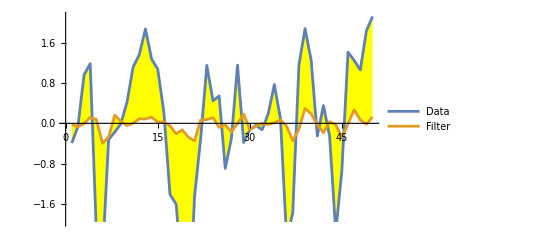

```mathematica
SeedRandom[99];
data=RandomFunction[ARMAProcess[{.1},{.6},1],{1,50}];
ar=EstimatedProcess[data,ARProcess[3]]
arFilter=KalmanFilter[ar,data]
ListLinePlot[{data,arFilter},Filling->{1->{2}},FillingStyle->Yellow,PlotLegends->{"Data","Filter"},ImageSize->400]
```